### Арифметические операции

#### Задание 1.1.

```mathematica
123+987
12.682+873.119
548-294
446.7321-29.013
35*721
35.0*721
57.29*48.117
21/35
46/13
46.0/13
257.34/868.014
21^35
7.68^12.3
```

1110

885.801

254

417.719

25235

25235.

2756.62

3/5

46/13

3.53846

0.29647

18952884486433699020098042171468383867092598701

7.76145×10^10

#### Задание 1.2

```mathematica
(1/5+3/11)^3-5*(2+4)
25.5/4+(2+4)/3^3
```

-4973674/166375

6.59722

#### Задание 1.3

```mathematica
586/46
N[586/46]
N[586/46, 25]
7^25
N[7^25]
N[7^25, 25]
```

293/23

12.7391

12.73913043478260869565217

1341068619663964900807

1.34107×10^21

1.341068619663964900807×10^21

#### Задание 1.4

```mathematica
389.65/4.7
N[389.65/4.7, 16]
```

82.9043

82.9043

#### Задание 1.5

```mathematica
N[π^3]
N[35!]
N[ⅇ^4.7]
N[Log[ⅇ^8]]
N[Log[3, 6561]]
N[Log[2*π], 30]
```

31.0063

1.03331×10^40

109.947

8.

8.

1.83787706640934548356065947281

#### Задание 1.6

```mathematica
Sin[π/6]
N[Sin[π/6]]
Sin[(13*π)/5]
N[Sin[(13*π)/5]]
Cos[30°]
N[Cos[30°]]
ArcCos[1/2]
N[ArcCos[1/2]]
ArcSin[.4]
N[ArcSin[.4]]
Tan[π/3]
N[Tan[π/3]]
ArcTan[3^(.5)]
N[ArcTan[3^(.5)]]
```

1/2

0.5

√(5/8+(√5)/8)

0.951057

(√3)/2

0.866025

π/3

1.0472

0.411517

0.411517

√3

1.73205

1.0472

1.0472

#### Задание 1.7

```mathematica
√(16)
√(x^2)
√(Abs[x])^2
```

4

√(x^2)

Abs[x]

#### Задание 1.8

```mathematica
?Degree
```

#### Задание 1.9

```mathematica
?*Log*
```

### Операторы присваивания. Подстановки.

#### Задание 2.1

```mathematica
x= RandomReal[]
y:=RandomReal[]
{x, x, x, x, x}
{y, y, y, y, y}
Clear[x,y]
```

0.284716

{0.284716,0.284716,0.284716,0.284716,0.284716}

{0.568734,0.655041,0.42924,0.740435,0.0845683}

#### Задание 2.2

```mathematica
x*ⅇ^x+Log[x]-y/. {x->1, y->2}
x*ⅇ^x+Log[x]-y/. {x->2a, y->b+c}
x^2+y^2+(Sin^2)[x]+(Cos^2)[x]+1.5/.{x->1, y->2}
x^2+y^2+(Sin^2)[x]+(Cos^2)[x]+1.5/. {x->2a, y->b+c}
```

-2+ⅇ

-b-c+2 a ⅇ^(2 a)+Log[2 a]

6.5+Cos^2[1]+Sin^2[1]

1.5+4 a^2+(b+c)^2+Cos^2[2 a]+Sin^2[2 a]

#### Задание 2.3

```mathematica
{x*ⅇ^-x, x^2, Sin[x], 2/(x^2-1)}/.x->{0.3, 0.6, 0.9, 1.2, 1.5, 1.8}
```

{{0.222245,0.329287,0.365913,0.361433,0.334695,0.297538},{0.09,0.36,0.81,1.44,2.25,3.24},{0.29552,0.564642,0.783327,0.932039,0.997495,0.973848},{-2.1978,-3.125,-10.5263,4.54545,1.6,0.892857}}

```mathematica
TableForm[{x, x*ⅇ^-x, x^2, Sin[x], 2/(x^2-1)}/.x->{0.3, 0.6, 0.9, 1.2, 1.5, 1.8}, TableHeadings->{{"x", "x*ⅇ^-x", "x^2", "Sin[x]", "2/x^2"}, None}]
```

x | 0.3 | 0.6 | 0.9 | 1.2 | 1.5 | 1.8
x*ⅇ^-x | 0.222245 | 0.329287 | 0.365913 | 0.361433 | 0.334695 | 0.297538
x^2 | 0.09 | 0.36 | 0.81 | 1.44 | 2.25 | 3.24
Sin[x] | 0.29552 | 0.564642 | 0.783327 | 0.932039 | 0.997495 | 0.973848
2/x^2 | -2.1978 | -3.125 | -10.5263 | 4.54545 | 1.6 | 0.892857

### Преобразование символьных выражений.

#### Задание 3.1

```mathematica
Factor[Expand[(x+1)^4-x^4-2x-1]]
```

2 x (1+x) (1+2 x)

```mathematica
Clear[x, y]
```

#### Задание 3.2

```mathematica
FactorTerms[12*y^2+6*x*y-6*x*z-12*y*z+30*y-30*z]
FactorTerms[12*y^2+6*x*y-6*x*z-12*y*z+30*y-30*z, x]
```

6 (5 y+x y+2 y^2-5 z-x z-2 y z)

6 (5+x+2 y) (y-z)

#### Задание 3.3

```mathematica
Collect[12*y^2+6*x*y-6*x*z-12*y*z+30*y-30*z, y]
Collect[12*y^2+6*x*y-6*x*z-12*y*z+
30*y-30*z, {y, z}]
Collect[12*y^2+6*x*y-6*x*z-12*y*z+30*y-30*z, {z, y}]
```

12 y^2+y (30+6 x-12 z)-30 z-6 x z

12 y^2+y (30+6 x-12 z)+(-30-6 x) z

(30+6 x) y+12 y^2+(-30-6 x-12 y) z

#### Задание 3.4

```mathematica
Cancel[(2*x^3+x*(5*x-1)-1)/(8*x^3-12*x^2+6*x-1)]
Together[(2x-1)-x2-5
(4x)^2-4*x+1-2*x^3+x*(5 x-1)-1]
Apart[(2*x-1)-(x)^2-5
(4x)^2-4*x+1-2*x^3+x*(5*x-1)-1]
```

(1+3 x+x^2)/(-1+2 x)^2

-1-5  (4x)^2-3 x+5 x^2-2 x^3-x2

-1-5  (4x)^2-(x)^2-3 x+5 x^2-2 x^3

#### Задание 3.5

```mathematica
TrigExpand[Cot[x]-Tan[x]-2 Tan[2*x]]
TrigFactor[Cot[x]-Tan[x]-2*Tan[2*x]]
TrigReduce[Cot[x]-Tan[x]-2*Tan[2*x]]
Simplify[Cot[x]-Tan[x]-2*Tan[2*x]]
TrigToExp[Sinh[x]+Cosh[x]]
Simplify[TrigToExp[Cot[x]-Tan[x]-2*Tan[2*x]]]
ExpToTrig[ⅇ^(ι*x)]
Simplify[ExpToTrig[1/16*ⅇ^(-4ιx)(1+ⅇ^(2ιx))^4]
```

(Cos[x]^2 Cot[x])/(Cos[x]^2-Sin[x]^2)-(6 Cos[x] Sin[x])/(Cos[x]^2-Sin[x]^2)+(Sin[x]^2 Tan[x])/(Cos[x]^2-Sin[x]^2)

Csc[π/4-x] Csc[x] Csc[π/4+x] Sec[x] Sin[π/4-2 x] Sin[π/4+2 x]

Cos[4 x] Csc[x] Sec[x] Sec[2 x]

4 Cot[4 x]

ⅇ^x

(4 ⅈ (1+ⅇ^(8 ⅈ x)))/(-1+ⅇ^(8 ⅈ x))

Cosh[x ι]+Sinh[x ι]

#### Задание 3.6

```mathematica
Simplify[(x^4-6 x^3-4 x^2-18x-21)/(x^3-7 x^2+3x-21)]
Simplify[1/8*(Cos[4*x]+4*Cos[2*x]+3)]
```

1+x

Cos[x]^4

#### Задание 3.7

```mathematica
Factor[(x^4-6 x^3-4 x^2-18x-21)/(x^3-7 x^2+3x-21)]
Factor[x^4-6 x^3-4 x^2-18x-21]/(x^3-7 x^2+3x-21)
■(x^4-6 x^3-4 x^2-18x-21)/(x^3-7 x^2+3x-21)
```

1+x

((-7+x) (1+x) (3+x^2))/(-21+3 x-7 x^2+x^3)

((-21-18 x-4 x^2-6 x^3+x^4) ■)/(-21+3 x-7 x^2+x^3)

### Операции математического анализа(ч.1)

#### Задание 4.1

```mathematica
Sum[k!*k, {k, 1, n}]
Sum[a*q^k, {k, 0,Infinity}]
Sum[1/(2k-1)^4, {k, 1, ∞}]
Sum[1/(2^k k), {k, 1, ∞}]
∑_(k=1)^(n-1) Sin[(π*k)/n]
∑_(k=1)^n (k^2+k-1)/((k+2)!)
∑_(k=1)^∞ 1/((2k+1)!)
∑_(k=1)^∞ (2k)/((2k+1)!)
```

-1+(1+n)!

a/(1-q)

π^4/96

Log[2]

Cot[π/(2 n)]

(-6-8 n-2 n^2+(3+n)!)/(2 (3+n)!)

-1+Sinh[1]

1/ⅇ

#### Задание 4.2

```mathematica
Sum[x^(n+2)/(n!),{x, 0, ∞}]
```

∑_(x=0)^∞ x^(2+n)/(n!)

#### Задание 4.3

```mathematica
Product[1+(-1)^(k+1)/(2k-1), {k, 1, ∞}]
Product[1-1/(2k-1)^2, {k, 2, ∞}]
x*∏_(k=1)^∞ (1+x^2/(k^2 π^2))
x*∏_(k=1)^∞ (1-x^2/(k^2 π^2))
```

√2

π/4

Sinh[x]

x Sinc[x]

#### Задание 4.4

```mathematica
Product[(1+x^(2n)), x]
```

#### Задание 4.5

```mathematica
Table[(x^2+1)/x, {x, 1, 5}]
Table[xⅇ^x, {x, 1, 5}]
Table[(x^2+y^2)/(2x), {x, 1, 5}]
```

{2,5/2,10/3,17/4,26/5}

{xⅇ,xⅇ^2,xⅇ^3,xⅇ^4,xⅇ^5}

{1/2 (1+y^2),1/4 (4+y^2),1/6 (9+y^2),1/8 (16+y^2),1/10 (25+y^2)}

#### Задание 4.6

```mathematica
TableForm[Table[{x, x^2, ⅇ^x//N, Log[x]//N}, {x, 1, 10}], TableHeadings->{None, {"x", "x^2", "ⅇ^x", "Log[x]"}}]
```

x | x^2 | ⅇ^x | Log[x]
1 | 1 | 2.71828 | 0.
2 | 4 | 7.38906 | 0.693147
3 | 9 | 20.0855 | 1.09861
4 | 16 | 54.5982 | 1.38629
5 | 25 | 148.413 | 1.60944
6 | 36 | 403.429 | 1.79176
7 | 49 | 1096.63 | 1.94591
8 | 64 | 2980.96 | 2.07944
9 | 81 | 8103.08 | 2.19722
10 | 100 | 22026.5 | 2.30259

#### Задание 4.7

```mathematica
TableForm[Table[{x, x^2, √x}, {x, 5, 9, 0.5}], TableHeadings->{None, {"x", "x^2", "x^(1/2)"}}, TableDirections->Row]
```

x | 5. | 5.5 | 6. | 6.5 | 7. | 7.5 | 8. | 8.5 | 9.
x^2 | 25. | 30.25 | 36. | 42.25 | 49. | 56.25 | 64. | 72.25 | 81.
x^(1/2) | 2.23607 | 2.34521 | 2.44949 | 2.54951 | 2.64575 | 2.73861 | 2.82843 | 2.91548 | 3.

#### Задание 4.8

```mathematica
TableForm[Table[n!m!, {n, 1, 5}, {m, 1, 7}], TableHeadings->{{"n=1", "n=2", "n=3", "n=4", "n=5"}, {"m=1", "m=2", "m=3", "m=4", "m=5", "m=6", "m=7"}}]
```

| m=1 | m=2 | m=3 | m=4 | m=5 | m=6 | m=7
n=1 | 1 | 2 | 6 | 24 | 120 | 720 | 5040
n=2 | 2 | 4 | 12 | 48 | 240 | 1440 | 10080
n=3 | 6 | 12 | 36 | 144 | 720 | 4320 | 30240
n=4 | 24 | 48 | 144 | 576 | 2880 | 17280 | 120960
n=5 | 120 | 240 | 720 | 2880 | 14400 | 86400 | 604800

### Операции математического анализа(ч.2)

#### Задание 5.1

```mathematica
Limit[(1-ⅇ^(-2t))/Log[1-3t], t->0]
Limit[(1-a^n)/(1-ⅇ^n), n->0]
Limit[(1-ⅇ^x)/(1-ⅇ^-x), x->0]
Limit[(1-x)^(1/(1-x)), x->∞]
Limit[(x-a)/Log[x-a+1], x->a]
Limit[(n^2-n^x)/(x-2), x->2]
```

-2/3

Log[a]

-1

1

1

-n^2 Log[n]

#### Задание 5.2

π/2

-π/2

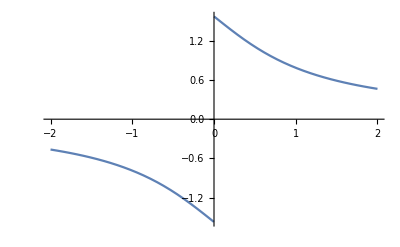

∞

-∞

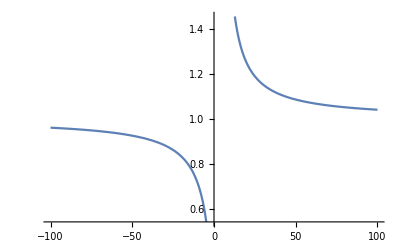

1

1

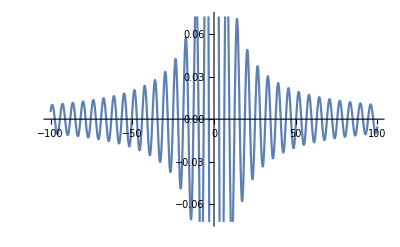

```mathematica
Limit[ArcTan[1/x], x->0, Direction->"FromAbove"]
Limit[ArcTan[1/x], x->0, Direction->"FromBelow"]
Plot[ArcTan[1/x], {x, -2, 2}]
Limit[x/(x-4), x->4, Direction->"FromAbove"]
Limit[x/(x-4), x->4, Direction->"FromBelow"]
Plot[x/(x-4), {x, -100, 100}]
Limit[Sin[x]/Abs[x], x->0,  Direction->"FromAbove"]
Limit[Sin[x]/Abs[x], x->0,  Direction->"FromAbove"]
Plot[Sin[x]/Abs[x], {x, -100, 100}]
```

#### Задание 5.3

```mathematica
Limit[2(a(1-ⅇ^-ax))/(2-ⅇ^-ax),x ->Infinity, Assumptions->a>0]
Limit[2*(a(1-ⅇ^-ax))/(2-ⅇ^-ax), x->Infinity, Assumptions->a<0]
```

(2 a (1-ⅇ^-ax))/(2-ⅇ^-ax)

(2 a (1-ⅇ^-ax))/(2-ⅇ^-ax)

```mathematica
Limit[a^x/x^a, x->Infinity, Assumptions->a>1]
Limit[a^x/x^a, x->Infinity, Assumptions->a≥0 && a ≤1]
```

∞

ConditionalExpression[0,Log[a]<0]

#### Задание 5.4

```mathematica
Series[f[x], {x, 0, 2}]
Series[f[x], {x, a, 2}]
```

f[0]+f'[0] x+1/2 f''[0] x^2+O[x]^3

f[a]+f'[a] (x-a)+1/2 f''[a] (x-a)^2+O[x-a]^3

#### Задание 5.5

```mathematica
Series[Sin[x]/Cos[x],{x, 0, 6}]
Series[Sinh[x]*Cosh[x], {x, 0, 6}]
Series[Log[x], {x, 0, 4}]
Collect[Series[Log[x], {x, 1, 4}], x]
```

x+x^3/3+(2 x^5)/15+O[x]^7

x+(2 x^3)/3+(2 x^5)/15+O[x]^7

Log[x]+O[x]^5

-25/12+4 x-3 x^2+(4 x^3)/3-x^4/4

#### Задание 5.6

```mathematica
Series[Exp[y]*Sin[x], {x, 0, 5}, {y, 0, 3}]
Normal[Series[Exp[y]*Sin[x], {x, 0, 5}, {y, 0, 3}]]
Collect[Series[Exp[y]*Sin[x], {x, 0, 5}, {y, 0, 3}], x]
Collect[Series[Exp[y]*Sin[x], {x, 0, 5}, {y, 0, 3}], y]
```

(1+y+y^2/2+y^3/6+O[y]^4) x+(-1/6-y/6-y^2/12-y^3/36+O[y]^4) x^3+(1/120+y/120+y^2/240+y^3/720+O[y]^4) x^5+O[x]^6

x^3 (-1/6-y/6-y^2/12-y^3/36)+x^5 (1/120+y/120+y^2/240+y^3/720)+x (1+y+y^2/2+y^3/6)

x^3 (-1/6-y/6-y^2/12-y^3/36)+x^5 (1/120+y/120+y^2/240+y^3/720)+x (1+y+y^2/2+y^3/6)

x-x^3/6+x^5/120+(x-x^3/6+x^5/120) y+(x/2-x^3/12+x^5/240) y^2+(x/6-x^3/36+x^5/720) y^3

#### Задание 5.7

```mathematica
D[Log[a/x], x]
D[Sinh[a*x], x]
D[x!, x]
```

-1/x

a Cosh[a x]

Gamma[1+x] PolyGamma[0,1+x]

```mathematica
D[(a*x^3+b*x-c), x]
D[((x-1)/(x+1)), x]
D[((Sin[x]+Cos[x])^2), x]
```

b+3 a x^2

-(-1+x)/(1+x)^2+1/(1+x)

2 (Cos[x]-Sin[x]) (Cos[x]+Sin[x])

#### Задание 5.8

```mathematica
D[a*x^7+b*x^5-c*x^3, {x, 7}]
D[(a*x^7+b*x^5-c*x^3), {x, 7}]
```

5040 a

5040 a

```mathematica
D[(y^2-1)/(y^3+1), {y, 5}]
D[((y^2-1)/(y^3+1)), {y, 5}]
```

(-1+y^2) (-(29160 y^10)/((1+y^3)^6)+(38880 y^7)/((1+y^3)^5)-(12960 y^4)/((1+y^3)^4)+(720 y)/((1+y^3)^3))+10 y ((1944 y^8)/((1+y^3)^5)-(1944 y^5)/((1+y^3)^4)+(360 y^2)/((1+y^3)^3))+20 (-(162 y^6)/((1+y^3)^4)+(108 y^3)/((1+y^3)^3)-6/((1+y^3)^2))

(-1+y^2) (-(29160 y^10)/((1+y^3)^6)+(38880 y^7)/((1+y^3)^5)-(12960 y^4)/((1+y^3)^4)+(720 y)/((1+y^3)^3))+10 y ((1944 y^8)/((1+y^3)^5)-(1944 y^5)/((1+y^3)^4)+(360 y^2)/((1+y^3)^3))+20 (-(162 y^6)/((1+y^3)^4)+(108 y^3)/((1+y^3)^3)-6/((1+y^3)^2))

```mathematica
D[Sinh[x*y], {x, 3}, {y, 5}]
D[(Sinh[x*y]), {x, 3}, {y, 5}]
```

60 x^2 Cosh[x y]+15 x^4 y^2 Cosh[x y]+60 x^3 y Sinh[x y]+x^5 y^3 Sinh[x y]

60 x^2 Cosh[x y]+15 x^4 y^2 Cosh[x y]+60 x^3 y Sinh[x y]+x^5 y^3 Sinh[x y]

#### Задание 5.9

```mathematica
D[Sin[x]^3+Cos[x^2], x]/. x->π/3//N
D[Sin[x]^3+Cos[x^2], {x, 2}] /.x->π/3//N
```

-0.738321

-4.43175

### Операции математического анализа(ч.3)

#### Задание 6.1

```mathematica
Integrate[ArcTan[Sqrt[x]]/(Sqrt[x]*(1+x)), x]
Integrate[(Sin[x]+Cos[x])/(Sin[x]-Cos[x])^(1/3), x, GeneratedParameters->C]
Integrate[1/(1-x^2)Log[(1+x)/(1-x)], x]//FullSimplify
∫Sin[x]*Log[Tan[x]]ⅆx
∫ⅇ^(2*x)*Sin[x]^2 ⅆx
∫ⅇ^(a*x)*Cos[b*x]ⅆx
```

ArcTan[√x]^2

C[1]+3/2 (-Cos[x]+Sin[x])^(2/3)

1/4 (-Log[2]^2+Log[4] Log[2-2 x]+Log[1+x]^2+Log[1/(1-x)] (Log[-4/(-1+x)]+2 Log[1+x]))

-Log[Cos[x/2]]+Log[Sin[x/2]]-Cos[x] Log[Tan[x]]

-1/8 ⅇ^(2 x) (-2+Cos[2 x]+Sin[2 x])

(ⅇ^(a x) (a Cos[b x]+b Sin[b x]))/(a^2+b^2)

#### Задание 6.2

```mathematica
D[(x*Abs[x]), x]
Integrate[x*Abs[x], x, Assumptions->x>0]
Assuming[x≤0, ∫x*Abs[x]ⅆx]
```

Abs[x]+x Abs'[x]

x^3/3

-x^3/3

#### Задание 6.3

```mathematica
Integrate[ArcSin[Sqrt[x/(1+x)]], {x, 0, 3}]
Integrate[ArcSin[Sqrt[x/(1+x)]], {x, 0, 3}]//N
```

-√3+(4 π)/3

2.45674

```mathematica
Integrate[1/(Sin[x]^4+Cos[x]^4), {x, 0, 2*π}]
Integrate[1/(Sin[x]^4+Cos[x]^4), {x, 0, 2*π}]//N
Integrate[1/(Sin[x]^4+Cos[x]^4), {x, 0, 2*π}, Assumptions->x ϵ Reals]
Integrate[1/(Sin[x]^4+Cos[x]^4), {x, 0, 2*π}, Assumptions->x ϵ Reals]//N
```

4 ⅈ π (-((1+Root0.0898-0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,1]0.08982027887554532)^3)/(8 √((1+2 ⅈ)-2 √(-1+ⅈ)) (-1+11 Root0.0898-0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,1]0.08982027887554532-3 (Root0.0898-0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,1]0.08982027887554532)^2+(Root0.0898-0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,1]0.08982027887554532)^3))+((1+Root0.0898+0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,2]0.08982027887554532)^3)/(8 √((1-2 ⅈ)-2 √(-1-ⅈ)) (-1+11 Root0.0898+0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,2]0.08982027887554532-3 (Root0.0898+0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,2]0.08982027887554532)^2+(Root0.0898+0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,2]0.08982027887554532)^3))-((1+Root1.91-4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,3]1.9101797211244547)^3)/(8 √((1-2 ⅈ)+2 √(-1-ⅈ)) (-1+11 Root1.91-4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,3]1.9101797211244547-3 (Root1.91-4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,3]1.9101797211244547)^2+(Root1.91-4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,3]1.9101797211244547)^3))+((1+Root1.91+4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,4]1.9101797211244547)^3)/(8 √((1+2 ⅈ)+2 √(-1+ⅈ)) (-1+11 Root1.91+4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,4]1.9101797211244547-3 (Root1.91+4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,4]1.9101797211244547)^2+(Root1.91+4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,4]1.9101797211244547)^3)))

8.88577+0. ⅈ

2 √2 π

8.88577

```mathematica
∫_0^2 Abs[1-x]ⅆx
```

1

```mathematica
∫_1^ⅇ (x*Log[x])^2 ⅆx
∫_1^ⅇ (x*Log[x])^2 ⅆx//N
```

1/27 (-2+5 ⅇ^3)

3.64547

```mathematica
∫_0^∞ (Sinh[x]+Cosh[x])/(ⅇ^(x^2))ⅆx
∫_0^∞ (Sinh[x]+Cosh[x])/(ⅇ^(x^2))ⅆx//N
```

1/2 ⅇ^(1/4) √π (1+Erf[1/2])

1.73023

#### Задание 6.4

```mathematica
Assuming[0<α<π,∫_-1^1 1/(x^2-2*x*Cos[α]+1)ⅆx]
```

1/2 π Csc[α]

```mathematica
Integrate[ⅇ^x/((a+ⅇ^x)^2), {x, -∞, +∞}]
Integrate[ⅇ^x/((a+ⅇ^x)^2), {x, -∞, +∞}, Assumptions->a≥0]
```

ConditionalExpression[1/a,Im[a]≠0||Re[a]==-1||Re[a]≥0]

1/a

```mathematica
Integrate[ⅇ^(-a*x)*Cos[b*x], {x, 0, ∞}]
Integrate[ⅇ^(-a*x)*Cos[b*x], {x, 0, ∞}, Assumptions->a≥0 && b ϵ Reals]
```

ConditionalExpression[a/(a^2+b^2),Re[a]>Im[b]]

ConditionalExpression[a/(a^2+b^2),a>Im[b]]

#### Задание 6.5

```mathematica
Integrate[x^(1/x)*ⅇ^x, {x, 1, 5}]//N
Integrate[Sin[Sin[x]], {x, 1, 2}]//N
∫_1^5 x^(1/x)*ⅇ^x ⅆx//N
∫_1^2 Sin[Sin[x]]ⅆx//N
```

204.435

0.81645

204.435

0.81645

#### Задание 6.6

```mathematica
∫∫∫(x*Log[x])^2 ⅆxⅆxⅆx
Integrate[Sin[x]*Sin[2*x]*Sin[3*x], x, x, x, x, x]
```

(x^5 (1489-2820 Log[x]+1800 Log[x]^2))/108000

(-7776 Cos[2 x]-243 Cos[4 x]+32 Cos[6 x])/995328

#### Задание 6.7

```mathematica
N[∫_0^2 ∫(x-1)/(x+1)ⅆxⅆx, 4]
```

-0.5917

```mathematica
N[Integrate[Sqrt[x-1]/x, {x, Log[2], ⅇ^2}, {x, Log[2], ⅇ^2}, {x, Log[2], ⅇ^2}],10]
```

119.5834854+6.2867052 ⅈ

```mathematica
Assuming[a>0&&b>a, ∫_a^b ∫(x-1)/(x+1)ⅆxⅆx]
```

-1/2 (a-b) (4+a+b)+2 (1+a) Log[1+a]-2 (1+b) Log[1+b]

#### Задание 6.8

```mathematica
∫_0^1 ∫_(x^2)^x (x+y^2)ⅆyⅆx
```

5/42

```mathematica
Integrate[(x+y^2), {x, 0, 1}, {y, x^2, x}]
```

5/42

```mathematica
∫_0^1 ∫_y^(√y) (x+y^2)ⅆxⅆy
```

5/42

### Списки, вектора, матрицы

#### Задание 7.1

```mathematica
v={{a, b}, {{ⅇ^2, Sin[x]}, y}}
```

{{a,b},{{ⅇ^2,Sin[x]},y}}

```mathematica
v⟦2,1,2⟧/v⟦1, 1⟧^v⟦1, 2⟧-v⟦2,1,1⟧*v⟦2,2⟧
```

-ⅇ^2 y+a^-b Sin[x]

```mathematica
Clear[v]
```

#### Задание 7.2

```mathematica
v1={a, b, c, d, e, f}
```

{a,b,c,d,e,f}

```mathematica
v2=Range[3, 23, 4]
```

{3,7,11,15,19,23}

```mathematica
m1=({{a, b, c}, {d, e, f}, {g, h, e}})
```

{{a,b,c},{d,e,f},{g,h,e}}

```mathematica
m2= ({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
v1+3
m1+7
```

{3+a,3+b,3+c,3+d,3+e,3+f}

{{7+a,7+b,7+c},{7+d,7+e,7+f},{7+g,7+h,7+e}}

```mathematica
v1-5
m1-6
```

{-5+a,-5+b,-5+c,-5+d,-5+e,-5+f}

{{-6+a,-6+b,-6+c},{-6+d,-6+e,-6+f},{-6+g,-6+h,-6+e}}

```mathematica
v1*4
m1*4
```

{4 a,4 b,4 c,4 d,4 e,4 f}

{{4 a,4 b,4 c},{4 d,4 e,4 f},{4 g,4 h,4 e}}

```mathematica
v1/2
m1/2
```

{a/2,b/2,c/2,d/2,e/2,f/2}

{{a/2,b/2,c/2},{d/2,e/2,f/2},{g/2,h/2,e/2}}

```mathematica
v1+v2
m1+m2
```

{3+a,7+b,11+c,15+d,19+e,23+f}

{{1+a,2+b,3+c},{4+d,5+e,6+f},{7+g,8+h,9+e}}

```mathematica
v1-v2
m1-m2
```

{-3+a,-7+b,-11+c,-15+d,-19+e,-23+f}

{{-1+a,-2+b,-3+c},{-4+d,-5+e,-6+f},{-7+g,-8+h,-9+e}}

```mathematica
v1/v2
m1/m2
```

{a/3,b/7,c/11,d/15,e/19,f/23}

{{a,b/2,c/3},{d/4,e/5,f/6},{g/7,h/8,e/9}}

```mathematica
v1*v2
m1*m2
```

{3 a,7 b,11 c,15 d,19 e,23 f}

{{a,2 b,3 c},{4 d,5 e,6 f},{7 g,8 h,9 e}}

```mathematica
Clear[v1,v2,m1,m2]
```

#### Задание 7.3

```mathematica
v1={1,3,5,2,6,4}
```

{1,3,5,2,6,4}

```mathematica
v2={2,7,5,8,1,3}
```

{2,7,5,8,1,3}

```mathematica
m1=({{1, 2, 3}, {6, 5, 4}, {1, 3, 5}})
```

{{1,2,3},{6,5,4},{1,3,5}}

```mathematica
m2=({{3, 2, 1}, {4, 5, 6}, {5, 3, 1}})
```

{{3,2,1},{4,5,6},{5,3,1}}

```mathematica
v2^2
m2^2
```

{4,49,25,64,1,9}

{{9,4,1},{16,25,36},{25,9,1}}

```mathematica
v1^(.5)
m1^(.5)
```

{1.,1.73205,2.23607,1.41421,2.44949,2.}

{{1.,1.41421,1.73205},{2.44949,2.23607,2.},{1.,1.73205,2.23607}}

```mathematica
ⅇ^v1//N
```

{2.71828,20.0855,148.413,7.38906,403.429,54.5982}

```mathematica
Sin[v2]//N
```

{0.909297,0.656987,-0.958924,0.989358,0.841471,0.14112}

```mathematica
Log[m1]//N
```

{{0.,0.693147,1.09861},{1.79176,1.60944,1.38629},{0.,1.09861,1.60944}}

```mathematica
Cosh[m2]//N
```

{{10.0677,3.7622,1.54308},{27.3082,74.2099,201.716},{74.2099,10.0677,1.54308}}

```mathematica
Clear[m1,m2,v1,v2]
```

#### Задание 7.4

```mathematica
v1={a,b,c}
```

{a,b,c}

```mathematica
v2={x,y,z}
```

{x,y,z}

```mathematica
v1*v2
```

{a x,b y,c z}

```mathematica
Dot[v1,v2]
```

a x+b y+c z

```mathematica
v1.v2
```

a x+b y+c z

```mathematica
Cross[v1,v2]
```

{-c y+b z,c x-a z,-b x+a y}

```mathematica
v1×v2
```

{-c y+b z,c x-a z,-b x+a y}

```mathematica
Clear[v1,v2]
```

#### Задание 7.5

```mathematica
A=({{Subscript[a, 11], Subscript[a, 12], Subscript[a, 13]}, {Subscript[a, 21], Subscript[a, 22], Subscript[a, 23]}, {Subscript[a, 31], Subscript[a, 32], Subscript[a, 33]}})
```

{{a_11,a_12,a_13},{a_21,a_22,a_23},{a_31,a_32,a_33}}

```mathematica
B=({{Subscript[b, 11], Subscript[b, 12], Subscript[b, 13]}, {Subscript[b, 21], Subscript[b, 22], Subscript[b, 23]}, {Subscript[b, 31], Subscript[b, 32], Subscript[b, 33]}})
```

{{b_11,b_12,b_13},{b_21,b_22,b_23},{b_31,b_32,b_33}}

```mathematica
A*B//MatrixForm
```

(a_11 b_11 | a_12 b_12 | a_13 b_13
a_21 b_21 | a_22 b_22 | a_23 b_23
a_31 b_31 | a_32 b_32 | a_33 b_33)

```mathematica
Dot[A,B]//MatrixForm
```

(a_11 b_11+a_12 b_21+a_13 b_31 | a_11 b_12+a_12 b_22+a_13 b_32 | a_11 b_13+a_12 b_23+a_13 b_33
a_21 b_11+a_22 b_21+a_23 b_31 | a_21 b_12+a_22 b_22+a_23 b_32 | a_21 b_13+a_22 b_23+a_23 b_33
a_31 b_11+a_32 b_21+a_33 b_31 | a_31 b_12+a_32 b_22+a_33 b_32 | a_31 b_13+a_32 b_23+a_33 b_33)

```mathematica
A.B//MatrixForm
```

(a_11 b_11+a_12 b_21+a_13 b_31 | a_11 b_12+a_12 b_22+a_13 b_32 | a_11 b_13+a_12 b_23+a_13 b_33
a_21 b_11+a_22 b_21+a_23 b_31 | a_21 b_12+a_22 b_22+a_23 b_32 | a_21 b_13+a_22 b_23+a_23 b_33
a_31 b_11+a_32 b_21+a_33 b_31 | a_31 b_12+a_32 b_22+a_33 b_32 | a_31 b_13+a_32 b_23+a_33 b_33)

```mathematica
Clear[A,B]
```

#### Задание 7.6

```mathematica
x=Range[0,2π,π/4]
```

{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

```mathematica
y=Sin[x]
```

{0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0}

```mathematica
L1={x,y}
```

{{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π},{0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0}}

```mathematica
TableForm[L1, TableHeadings->{{"x", "y"},None}]
```

x | 0 | π/4 | π/2 | (3 π)/4 | π | (5 π)/4 | (3 π)/2 | (7 π)/4 | 2 π
y | 0 | 1/(√2) | 1 | 1/(√2) | 0 | -1/(√2) | -1 | -1/(√2) | 0

```mathematica
L2=Transpose[L1]
```

{{0,0},{π/4,1/(√2)},{π/2,1},{(3 π)/4,1/(√2)},{π,0},{(5 π)/4,-1/(√2)},{(3 π)/2,-1},{(7 π)/4,-1/(√2)},{2 π,0}}

```mathematica
TableForm[L2, TableHeadings->{None,{"x", "y"}}]
```

x | y
0 | 0
π/4 | 1/(√2)
π/2 | 1
(3 π)/4 | 1/(√2)
π | 0
(5 π)/4 | -1/(√2)
(3 π)/2 | -1
(7 π)/4 | -1/(√2)
2 π | 0

```mathematica
L2⟦6⟧
```

{(5 π)/4,-1/(√2)}

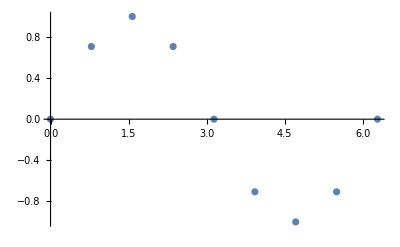

```mathematica
ListPlot[L2]
```

```mathematica
Clear[x,y,L1,L2]
```

#### Задание 7.7

```mathematica
B=({{1.5, -0.8, 4.25}, {1.2, 7.18, -3.2}, {0.5, -1.5, 7.1}})
```

{{1.5,-0.8,4.25},{1.2,7.18,-3.2},{0.5,-1.5,7.1}}

```mathematica
A=({{5.1}, {4.2}, {-1.2}})
```

{{5.1},{4.2},{-1.2}}

```mathematica
x=LinearSolve[B,A]
```

{{4.8872},{-0.508433},{-0.620598}}

```mathematica
B.x ==A
```

True

```mathematica
x⟦1⟧+x⟦2⟧+x⟦3⟧
```

{3.75817}

```mathematica
Clear[A,B,x]
```

### Простейшее описание функций

#### Задание 8.1

```mathematica
F1[x_]=x^3
```

x^3

```mathematica
F2[h_]=h^3
```

h^3

```mathematica
F1[x]/.x->{2, y,3b,Sin[x]}
F2[x]/.x->{2, y,3b,Sin[x]}
```

{8,y^3,27 b^3,Sin[x]^3}

{8,y^3,27 b^3,Sin[x]^3}

```mathematica
D[F1[x], x, x]
```

6 x

```mathematica
∫∫∫F1[x]ⅆxⅆxⅆx
```

x^6/120

```mathematica
Clear[F1, F2]
```

#### Задание 8.2

```mathematica
f1[x_]=Length[x]
```

0

```mathematica
f2[x_]:=Length[x]
```

```mathematica
f1[{8,7,6,5,4,3}]
f2[{8,7,6,5,4,3}]
```

0

6

```mathematica
Clear[f1,f2]
```

#### Задание 8.3

```mathematica
G1[x_, y_]=ⅇ^(-3x)Cos[y^2]
```

ⅇ^(-3 x) Cos[y^2]

```mathematica
G2[x_, y_]=D[G1[x, y], {x,3},{y,5}]
```

-27 ⅇ^(-3 x) (160 y^3 Cos[y^2]+120 y Sin[y^2]-32 y^5 Sin[y^2])

```mathematica
G3[x_,y_]=Integrate[G1[x, y], x,y,y]
```

1/6 ⅇ^(-3 x) (-√(2 π) y FresnelC[√(2/π) y]+Sin[y^2])

```mathematica
TableForm[Table[G1[x,y]//N, {x,0,3},{y,0,5}],TableHeadings->{{"x=0","x=1","x=2","x=3"}, {"y=0","y=1","y=2","y=3","y=4","y=5"}}]
TableForm[Table[G2[x,y]//N, {x,0,3},{y,0,5}],TableHeadings->{{"x=0","x=1","x=2","x=3"}, {"y=0","y=1","y=2","y=3","y=4","y=5"}}]
TableForm[Table[G3[x,y]//N, {x,0,3},{y,0,5}],TableHeadings->{{"x=0","x=1","x=2","x=3"}, {"y=0","y=1","y=2","y=3","y=4","y=5"}}]
```

| y=0 | y=1 | y=2 | y=3 | y=4 | y=5
x=0 | 1. | 0.540302 | -0.653644 | -0.91113 | -0.957659 | 0.991203
x=1 | 0.0497871 | 0.0269001 | -0.032543 | -0.0453625 | -0.0476791 | 0.0493491
x=2 | 0.00247875 | 0.00133928 | -0.00162022 | -0.00225847 | -0.0023738 | 0.00245695
x=3 | 0.00012341 | 0.0000666786 | -0.000080666 | -0.000112442 | -0.000118185 | 0.000122324

| y=0 | y=1 | y=2 | y=3 | y=4 | y=5
x=0 | 0. | -4333.44 | 6569.93 | 188794. | 13786.5 | -890455.
x=1 | 0. | -215.749 | 327.097 | 9399.48 | 686.389 | -44333.2
x=2 | 0. | -10.7415 | 16.2852 | 467.972 | 34.1733 | -2207.22
x=3 | 0. | -0.534789 | 0.810794 | 23.299 | 1.70139 | -109.891

| y=0 | y=1 | y=2 | y=3 | y=4 | y=5
x=0 | 0. | -0.161263 | -0.433775 | -0.634177 | -0.840598 | -1.04117
x=1 | 0. | -0.00802881 | -0.0215964 | -0.0315738 | -0.0418509 | -0.0518368
x=2 | 0. | -0.000399731 | -0.00107522 | -0.00157197 | -0.00208363 | -0.0025808
x=3 | 0. | -0.0000199014 | -0.0000535321 | -0.0000782637 | -0.000103738 | -0.000128491

```mathematica
G3[x_, y_] := Integrate[G1[x, y], x,y,y]
```

```mathematica
TableForm[Table[G3[x,y]//N, {x,0,3},{y,0,5}],TableHeadings->{{"x=0","x=1","x=2","x=3"}, {"y=0","y=1","y=2","y=3","y=4","y=5"}}]
```

Integrate::ilim: Invalid integration variable or limit(s) in 0.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

| y=0 | y=1 | y=2 | y=3 | y=4 | y=5
x=0 | ∫∫∫1ⅆ0ⅆ0ⅆ0 | ∫∫∫Cos[1]ⅆ1ⅆ1ⅆ0 | ∫∫∫Cos[4]ⅆ2ⅆ2ⅆ0 | ∫∫∫Cos[9]ⅆ3ⅆ3ⅆ0 | ∫∫∫Cos[16]ⅆ4ⅆ4ⅆ0 | ∫∫∫Cos[25]ⅆ5ⅆ5ⅆ0
x=1 | ∫∫∫1/ⅇ^3 ⅆ0ⅆ0ⅆ1 | ∫∫∫Cos[1]/ⅇ^3 ⅆ1ⅆ1ⅆ1 | ∫∫∫Cos[4]/ⅇ^3 ⅆ2ⅆ2ⅆ1 | ∫∫∫Cos[9]/ⅇ^3 ⅆ3ⅆ3ⅆ1 | ∫∫∫Cos[16]/ⅇ^3 ⅆ4ⅆ4ⅆ1 | ∫∫∫Cos[25]/ⅇ^3 ⅆ5ⅆ5ⅆ1
x=2 | ∫∫∫1/ⅇ^6 ⅆ0ⅆ0ⅆ2 | ∫∫∫Cos[1]/ⅇ^6 ⅆ1ⅆ1ⅆ2 | ∫∫∫Cos[4]/ⅇ^6 ⅆ2ⅆ2ⅆ2 | ∫∫∫Cos[9]/ⅇ^6 ⅆ3ⅆ3ⅆ2 | ∫∫∫Cos[16]/ⅇ^6 ⅆ4ⅆ4ⅆ2 | ∫∫∫Cos[25]/ⅇ^6 ⅆ5ⅆ5ⅆ2
x=3 | ∫∫∫1/ⅇ^9 ⅆ0ⅆ0ⅆ3 | ∫∫∫Cos[1]/ⅇ^9 ⅆ1ⅆ1ⅆ3 | ∫∫∫Cos[4]/ⅇ^9 ⅆ2ⅆ2ⅆ3 | ∫∫∫Cos[9]/ⅇ^9 ⅆ3ⅆ3ⅆ3 | ∫∫∫Cos[16]/ⅇ^9 ⅆ4ⅆ4ⅆ3 | ∫∫∫Cos[25]/ⅇ^9 ⅆ5ⅆ5ⅆ3

```mathematica
Clear[G1,G2,G3]
```

#### Задание 8.4

```mathematica
F[x_,y_]=y^3 Cos[x]
```

y^3 Cos[x]

```mathematica
Integrate[F[x,y], {x,0,2}, {y, (2x-x^2)^(1/2),(2x)^(1/2)}]
```

6+10 Cos[2]-2 Sin[2]

```mathematica
∫_0^2 ∫_((2x-x^2)^(1/2))^((2x)^(1/2)) F[x,y]ⅆyⅆx
```

6+10 Cos[2]-2 Sin[2]

```mathematica
Clear[F]
```

### Описание сложных функций

#### Задание 9.1

```mathematica
G1[x_/;Cos[x]>1/2]:=x^2
```

```mathematica
G2[x_]:=x^2/;Cos[x]>1/2
```

```mathematica
G1[1/2]
G1[1/10]
G1[3/2]
```

1/4

1/100

G1[3/2]

```mathematica
G2[1/2]
G2[1/10]
G2[3/2]
```

1/4

1/100

G2[3/2]

```mathematica
Clear[G1,G2]
```

#### Задание 9.2

```mathematica
g[x_Integer]=3 x^3-Tan[x]
```

3 x^3-Tan[x]

```mathematica
g[x]/.x->{2,0.5,Cos[x],"текст",15}
```

{26.185,-0.171302,3. Cos[x]^3-1. Tan[Cos[x]],3. текст^3-1. Tan[текст],10125.9}/;{2,0.5,Cos[x],текст,15} ϵ Integer

```mathematica
Clear[g]
```

#### Задание 9.3

```mathematica
U1[x_List/;Length[x]≤4]=Log[x^2-x]
```

Log[-x+x^2]

```mathematica
U2[x_List]=Log[x^2-x]/;Length[x]≤4
```

Log[-x+x^2]/;Length[x]≤4

```mathematica
U1[2]
U1[{2}]
U1[{1,2,a,4}]
U1[{1,2,a,4,t}]
```

U1[2]

{Log[2]}

{-∞,Log[2],Log[-a+a^2],Log[12]}

U1[{1,2,a,4,t}]

```mathematica
U2[2]
U2[{2}]
U2[{1,2,a,4}]
U2[{1,2,a,4,t}]
```

Log[2]/;2 ϵ List&&Length[2]≤4

{Log[2]}/;{2} ϵ List&&Length[{2}]≤4

{-∞,Log[2],Log[-a+a^2],Log[12]}/;{1,2,a,4} ϵ List&&Length[{1,2,a,4}]≤4

{-∞,Log[2],Log[-a+a^2],Log[12],Log[-t+t^2]}/;{1,2,a,4,t} ϵ List&&Length[{1,2,a,4,t}]≤4

```mathematica
Clear[U1,U2]
```

#### Задание 9.4

```mathematica
W[x_List]=Sin[x]^2
```

Sin[x]^2

```mathematica
W[x_Integer]=x^3+10
```

10+x^3

```mathematica
W[x_Real]=ArcTan[x]/x
```

ArcTan[x]/x

```mathematica
W[x_Complex]=(Re[x]+Im[x])/2
```

1/2 (Im[x]+Re[x])

```mathematica
W[{1,2,3,4,5,6}]
W[{a,b,c,d}]
W[3]
W[4.7]
W[1+2ⅈ]
```

{Sin[1]^2,Sin[2]^2,Sin[3]^2,Sin[4]^2,Sin[5]^2,Sin[6]^2}

{Sin[a]^2,Sin[b]^2,Sin[c]^2,Sin[d]^2}

37

0.289608

3/2

```mathematica
Clear[W]
```

#### Задание 9.5

```mathematica
H[x_Integer]=x
```

x

```mathematica
H[x_Real]=Round[x]
```

Round[x]

```mathematica
H[2]
H[-5]
H[3.4]
H[-1.7]
```

2

-5

3

-2

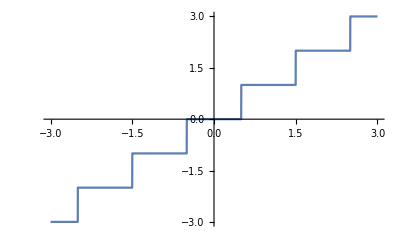

```mathematica
Plot[H[x], {x, -3, 3}]
```

#### Задание 9.6

```mathematica
W[x_/;0≤x≤5]=x^2
W[x_/;5≤x≤10]=(x-5)^2
W[x_/;10≤x≤15]=(x-10)^2
W[x_/;x≥15]=0
```

x^2

(-5+x)^2

(-10+x)^2

0

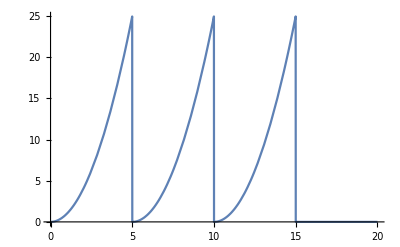

```mathematica
Plot[W[x], {x, 0,20}]
```

```mathematica
Clear[W]
```

#### Задание 9.7

```mathematica
Y[x_]=Piecewise[{{0, x<-2}, {x+2, -2≤x<0},{-x+2,0≤x<2},{0,x≥2}}]
```

Piecewise[{{0, x<-2}, {2+x, -2≤x<0}, {2-x, 0≤x<2}, {0, True}}]

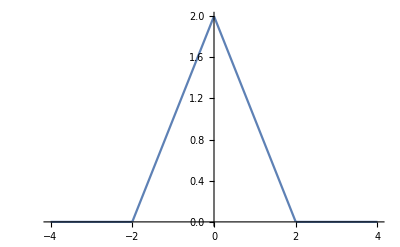

```mathematica
Plot[Y[x], {x, -4, 4}]
```

```mathematica
Clear[Y]
```

#### Задание 9.8

```mathematica
y1[x_]=Piecewise[{{1, -4≤x<-2}, {2, -2≤x<0}, {1, 0≤x<2}, {2, 2≤x≤4}}];
```

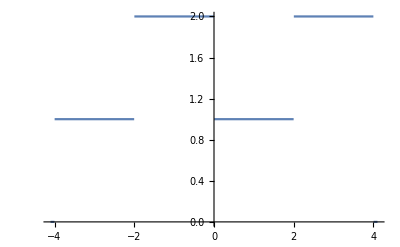

```mathematica
Plot[y1[x], {x, -4.1, 4.1}]
```

```mathematica
y2[x_/;-4≤x<-2]:=1
```

```mathematica
y2[x_/;-2≤x<0]:=2
```

```mathematica
y2[x_/;0≤x<2]:=1
```

```mathematica
y2[x_/;2≤x≤4]:=2
```

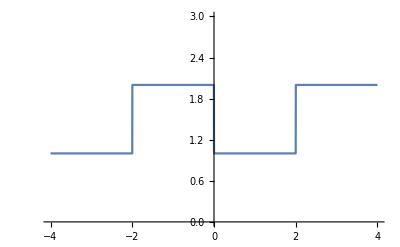

```mathematica
Plot[y2[x], {x, -4.1, 4.1}, PlotRange->{0,3}]
```

```mathematica
Clear[y1,y2]
```

#### Задание 9.9

```mathematica
Y[x_]=Piecewise[{{0, (-1≤x≤1 && 3<=Abs[x]≤4)}, {3+x, -3<x≤-2}, {-x-1, -2<x≤-1}, {x-1, 1<x≤2}, {-x+3, 2<x≤3}}]
```

Piecewise[{{0, -1≤x≤1&&3≤Abs[x]≤4}, {3+x, -3<x≤-2}, {-1-x, -2<x≤-1}, {-1+x, 1<x≤2}, {3-x, 2<x≤3}, {0, True}}]

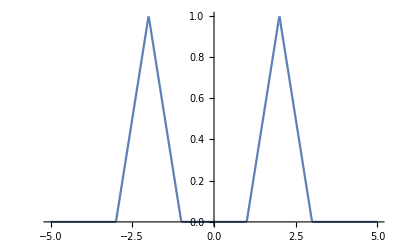

```mathematica
Plot[Y[x], {x, -5,5}]
```

```mathematica
Clear[Y]
```

### Графическая функция Plot и её опции

#### Задание 10.1

```mathematica
y[x_]=x*ⅇ^-x;
```

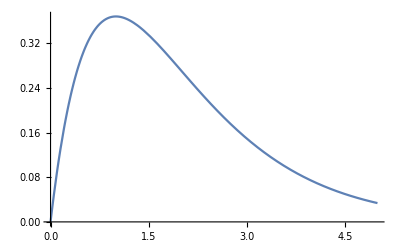

```mathematica
Plot[y[x], {x, 0,5}]
```

```mathematica
y2[x_]=30/(10+x^4);
```

```mathematica
y3[x_]=10 xⅇ^-x;
```

```mathematica
y1[x_]=Piecewise[{{2, 0≤x<2}, {-x+4, 2≤x<4}, {2x-8, 4≤x<6}, {-x+10, 6≤x<8}, {2, 8≤x<10}}]
```

Piecewise[{{2, 0≤x<2}, {4-x, 2≤x<4}, {-8+2 x, 4≤x<6}, {10-x, 6≤x<8}, {2, 8≤x<10}, {0, True}}]

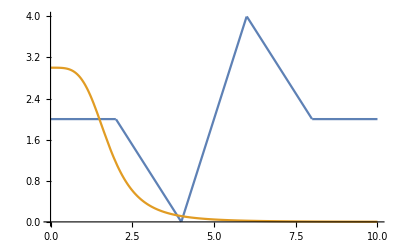

```mathematica
Plot[{y1[x], y2[x], y3[x]}, {x, 0,10}]
```

```mathematica
Clear[y1,y2,y3]
```

#### Задание 10.2

```mathematica
y[x_]=Log[4-2x]+x^2-2;
```

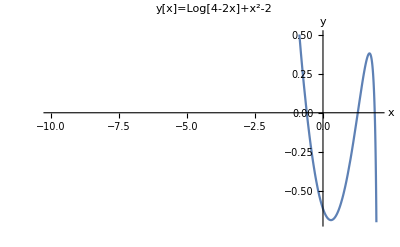

```mathematica
Plot[y[x], {x, -10,10}, PlotRange->{-0.7,0.5}, PlotLabel->"y[x]=Log[4-2x]+x^2-2", AxesLabel->{x,y}]
```

```mathematica
Clear[y]
```

#### Задание 10.3

```mathematica
y[x_]=ⅇ^-x/((1+ⅇ^(-2x))2-x);
```

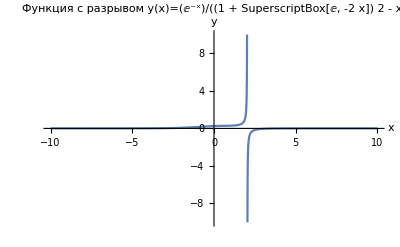

```mathematica
Plot[y[x], {x, -10, 10}, PlotRange->{-10,10}, PlotLabel->"Функция с разрывом y(x)=ⅇ^-x/((1 + SuperscriptBox[ⅇ, -2 x]) 2 - x)", AxesLabel->{Style["x", FontSize->16],Style["y", FontSize->16]}]
```

```mathematica
Clear[y]
```

#### Задание 10.4

```mathematica
y[x_]=Sin[x]/x;
```

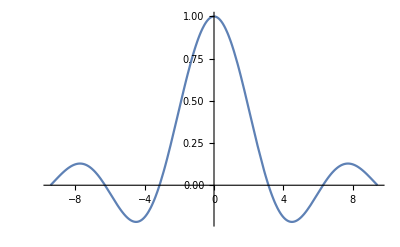

```mathematica
Plot[y[x], {x,-3π, 3π}]
```

```mathematica
Plot[y[x], {x,-3π, 3π}, Axes->{False, True}]
```

-Graphics-

```mathematica
Plot[y[x], {x,-3π, 3π}, Axes->{True, False}]
```

-Graphics-

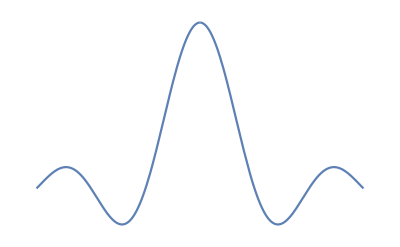

```mathematica
Plot[y[x], {x,-3π, 3π}, Axes->{False, False}]
```

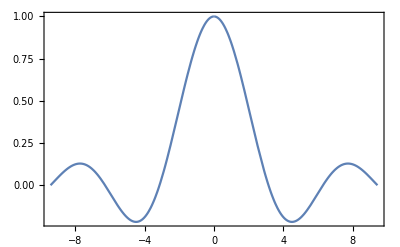

```mathematica
Plot[y[x], {x,-3π, 3π}, Frame->True ,Axes->{False, False}]
```

```mathematica
Plot[y[x], {x, -3π, 3π}, Axes->{False, False}, Frame->{{True, False}, {True, False}}]
```

-Graphics-

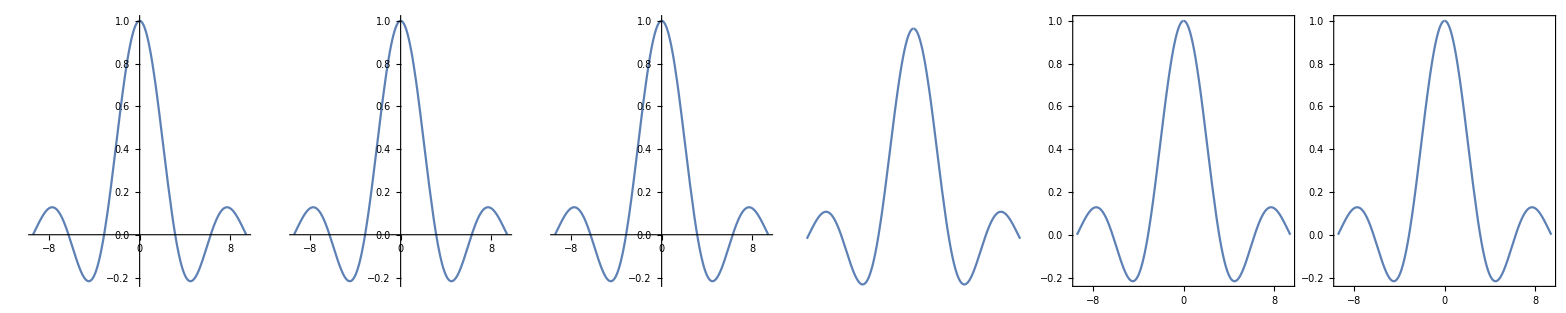

```mathematica
TableForm[Table[{Plot[y[x], {x,-3π, 3π}], Plot[y[x], {x,-3π, 3π}, Axes->{False, True}], Plot[y[x], {x,-3π, 3π}, Axes->{True, False}], Plot[y[x], {x,-3π, 3π}, Axes->{False, False}], Plot[y[x], {x,-3π, 3π}, Frame->True ,Axes->{False, False}], Plot[y[x], {x, -3π, 3π}, Axes->{False, False}, Frame->{{True, False}, {True, False}}]},1]]
```

```mathematica
Clear[y]
```

#### Задание 10.5, 10.6

```mathematica
y1[x_]=Sin[x]/x;
```

```mathematica
y2[x_]=Cos[x];
```

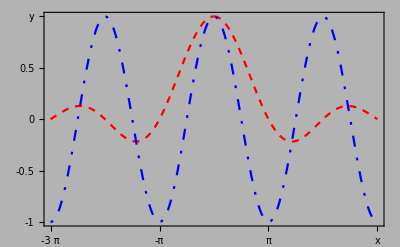

```mathematica
Plot[{y1[x], y2[x]}, {x, -3π, 3π}, BaseStyle->{FontFamily->"Arial", FontSize->16}, Ticks->{{-3π,-2π,-1π,0,π,1π,2π,{3π, "y"}}, {-1, -0.5,0,0.5,1}}, AxesStyle->Thickness->0.005, PlotStyle->{{RGBColor[255,0,0], Dashed}, {RGBColor[0,0,255], Dashing[{0.005,0.02,0.02,0.02}]}}, Axes->{False, False}, Frame->{True}, PlotRange->{{-3π, 3π}, {-1,1}}, FrameTicks->{{{-1,-0.5,0,0.5,{1,"y"}}, None}, {{-3π,-2π,-1π,0,π,2π,{3π,"x"}}, None}}, GridLines->{{-2π,-1π,0,π,1π,2π}, {-0.5,0,0.5}}, Background->GrayLevel[.7]]
```

```mathematica
Clear[y1,y2]
```

### Специальные виды двумерных графиков

#### Задание 11.1

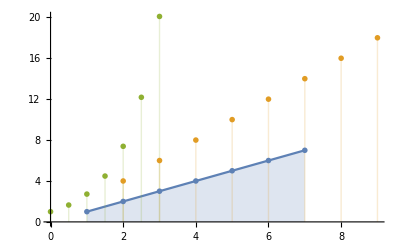

```mathematica
ListPlot[{{{1,1}, {2,2},{3,3}, {4,4}, {5,5}, {6,6}, {7,7}}, {{2,4}, {3,6},{4,8}, {5,10},{6,12},{7,14},{8,16},{9,18}},{{0,1},{0.5,ⅇ^0.5},{1,ⅇ^1},{1.5,ⅇ^1.5},{2,ⅇ^2},{2.5,ⅇ^2.5},{3,ⅇ^3}}},PlotRange->All,Joined->{True,False,False},Filling->Axis,PlotStyle->{PointSize[0.015],PointSize[0.02],PointSize[0.025]}, PlotMarkers->{{"1",15},{"2",15},{"3",15}}]
```

#### Задание 11.2

```mathematica
r[ϕ_]=Sin[ϕ];
```

```mathematica
g[ϕ_]=Cos[ϕ];
```

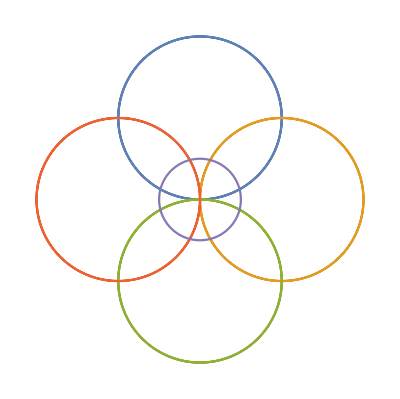

```mathematica
PolarPlot[{r[ϕ],g[ϕ],r[-ϕ],g[ϕ-π],1/4},{ϕ,0,2π},Axes->False]
```

```mathematica
Clear[r,g]
```

```mathematica
r[ϕ_]=1-Sin[ϕ];
```

```mathematica
g[ϕ_]=ⅇ^Cos[ϕ]-2Cos[4ϕ]+Sin[(2ϕ-π)/24]^5;
```

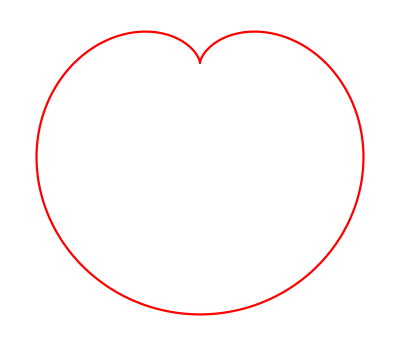

```mathematica
PolarPlot[r[ϕ],{ϕ,0,2π},Axes->False,PlotStyle->Red]
```

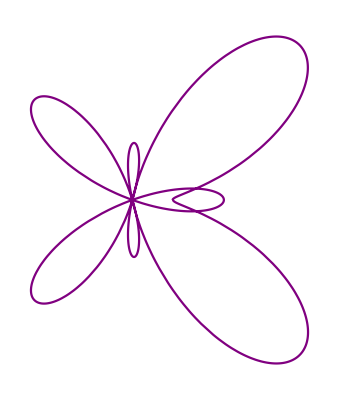

```mathematica
PolarPlot[g[ϕ],{ϕ,0,2π},Axes->False,PlotStyle->Purple]
```

```mathematica
Clear[r,g]
```

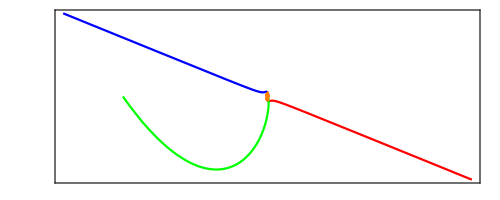

```mathematica
PolarPlot[{-3((x+3)/(3-x))^(1/2),3((x+3)/(3-x))^(1/2),ⅇ^(-2x),5Sin[5x+1]},{x,-π,π},Axes->False,Frame->True,FrameTicks->None,PlotStyle->{Red,Blue,Green,Orange}]
```

#### Задание 11.3

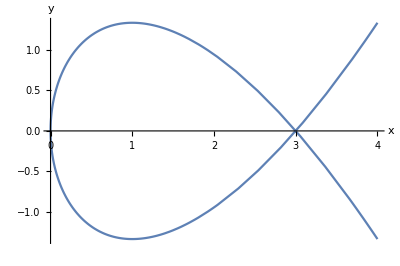

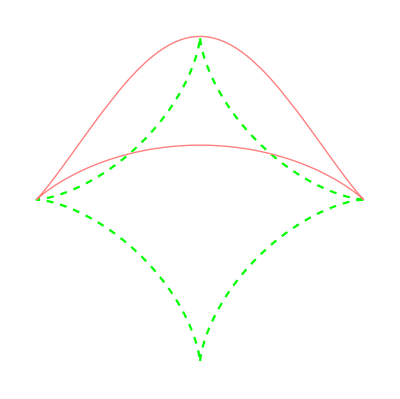

```mathematica
ParametricPlot[{t^2,2/3 t(3-t^2)},{t,-2,2},AxesLabel->{Style["x",FontSize->14],Style["y",FontSize->14]}]
ParametricPlot[{{3 Cos[t]^3,3 Sin[t]^3}, {3Sin[t],3(Cos[t]^2*(2+Cos[t]))/(3+Sin[t]^2)}},{t,0,2π}, Axes->False, PlotStyle->{{Green,Dashed},{Pink,Thick}}]
```

#### Задание 11.4

```mathematica
f[x_,y_]=Cos[x]+Cos[y];
```

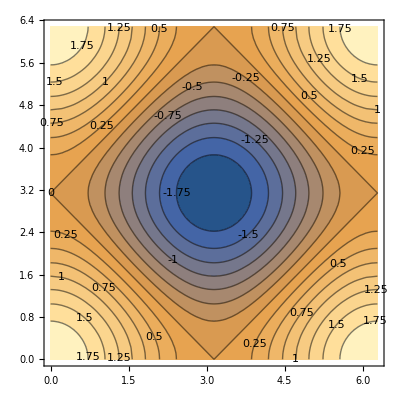

```mathematica
ContourPlot[f[x,y],{x,0,2π},{y,0,2π},Contours->15, ContourLabels->All]
```

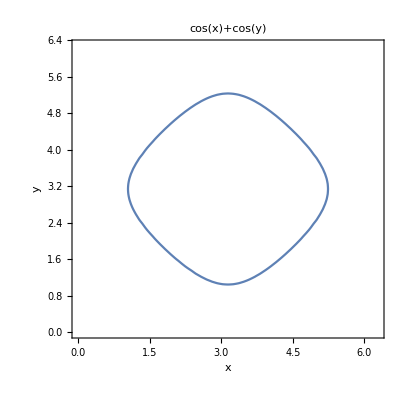

```mathematica
ContourPlot[f[x,y]==-1/2,{x,0,2π},{y,0,2π},FrameLabel->{"x","y"},PlotLabel->"cos(x)+cos(y)", FrameStyle->FontSize->14]
```

```mathematica
Clear[f]
```

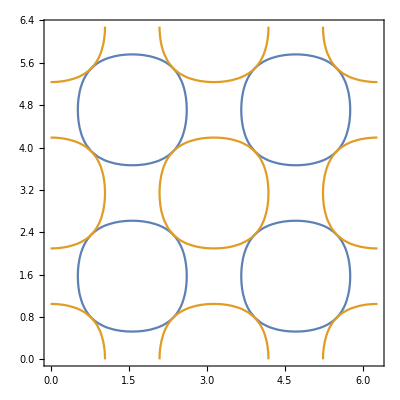

```mathematica
ContourPlot[{Abs[Sin[x]Sin[y]]==1/2,Abs[Cos[x]Cos[y]]==1/2}, {x,0,2π},{y,0,2π}]
```

```mathematica
y[x_]=x^2-4x+7;
```

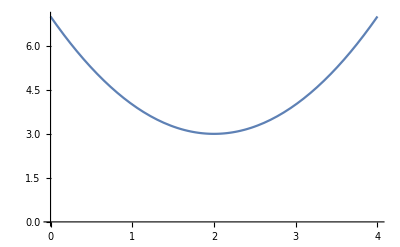

```mathematica
gr1=Plot[y[x], {x,0,4},AxesOrigin->{0,0}]
```

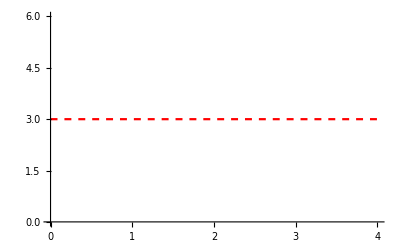

```mathematica
gr2=Plot[3,{x,0,4},PlotStyle->{Red,Dashed}]
```

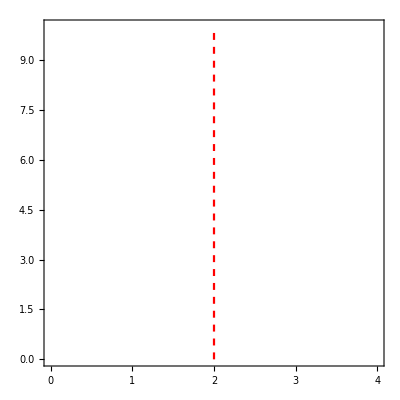

```mathematica
gr3=ContourPlot[x==2,{x,0,4},{y,0,10},ContourStyle->{Red,Dashed}]
```

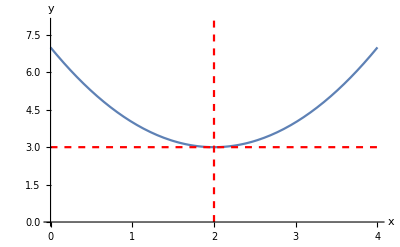

```mathematica
Show[gr1,gr2,gr3,PlotRange->{{0,4},{0,8}},AxesLabel->{"x","y"},AxesStyle->FontSize->14]
```

```mathematica
Clear[gr1,gr2,gr3,y]
```

### Решение алгебраических и трансцендентных уравнений и неравенств

#### Задание 12.1

```mathematica
XX=x/.Solve[a*x^2+b*x+c==0,x]
```

{(-b-√(b^2-4 a c))/(2 a),(-b+√(b^2-4 a c))/(2 a)}

```mathematica
a*x^2+b*x+c/.x->XX//Simplify
```

{0,0}

```mathematica
Expand[Simplify[a(x-XX⟦1⟧)(x-XX⟦2⟧)]]
```

```mathematica
c+b x+a x^2
```

```mathematica
Clear[XX]
```

```mathematica
x/.Solve[4 x^3+6 x^2+3x-4==0,x]
x/.Solve[4 x^3+6 x^2+3x-4==0,x]//N
x/.NSolve[4 x^3+6 x^2+3x-4==0,x,20]
```

{Root0.540Root[-4+3 #1+6 #1^2+4 #1^3&,1]0.540041911525952,Root-1.02-0.901 ⅈRoot[-4+3 #1+6 #1^2+4 #1^3&,2]-1.020020955762976,Root-1.02+0.901 ⅈRoot[-4+3 #1+6 #1^2+4 #1^3&,3]-1.020020955762976}

{0.540042,-1.02002-0.900703 ⅈ,-1.02002+0.900703 ⅈ}

{-1.0200209557629760286-0.900702716382002045 ⅈ,-1.0200209557629760286+0.900702716382002045 ⅈ,0.54004191152595205727}

```mathematica
x/.Solve[2*x^20+x^12==0,x]
x/.NSolve[2*x^20+x^12==0,x]
x/.NSolve[2*x^20+x^12==0,x,20]
```

{0,0,0,0,0,0,0,0,0,0,0,0,-(-1/2)^(1/8),(-1/2)^(1/8),-(-1)^(3/8)/2^(1/8),(-1)^(3/8)/2^(1/8),-(-1)^(5/8)/2^(1/8),(-1)^(5/8)/2^(1/8),-(-1)^(7/8)/2^(1/8),(-1)^(7/8)/2^(1/8)}

{-0.847201-0.350922 ⅈ,-0.847201+0.350922 ⅈ,-0.350922-0.847201 ⅈ,-0.350922+0.847201 ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.350922-0.847201 ⅈ,0.350922+0.847201 ⅈ,0.847201-0.350922 ⅈ,0.847201+0.350922 ⅈ}

{-0.8472012667468914604-0.3509222547462286622 ⅈ,-0.8472012667468914604+0.3509222547462286622 ⅈ,-0.3509222547462286622-0.8472012667468914604 ⅈ,-0.3509222547462286622+0.8472012667468914604 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0.3509222547462286622-0.8472012667468914604 ⅈ,0.3509222547462286622+0.8472012667468914604 ⅈ,0.8472012667468914604-0.3509222547462286622 ⅈ,0.8472012667468914604+0.3509222547462286622 ⅈ}

```mathematica
x/.Solve[x^5+x^4+2 x^3-x^2+4x+3==0,x]
x/.NSolve[x^5+x^4+2 x^3-x^2+4x+3==0,x]
x/.NSolve[x^5+x^4+2 x^3-x^2+4x+3==0,x,20]
```

{Root-0.580Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,1]-0.5801299881742208,Root-0.992-1.52 ⅈRoot[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,2]-0.9920483073775709,Root-0.992+1.52 ⅈRoot[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,3]-0.9920483073775709,Root0.782-0.981 ⅈRoot[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,4]0.7821133014646813,Root0.782+0.981 ⅈRoot[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,5]0.7821133014646813}

{-0.992048-1.51736 ⅈ,-0.992048+1.51736 ⅈ,-0.58013,0.782113-0.980699 ⅈ,0.782113+0.980699 ⅈ}

{-0.9920483073775709379-1.5173550338934896082 ⅈ,-0.9920483073775709379+1.5173550338934896082 ⅈ,-0.58012998817422074742,0.7821133014646813116-0.9806988137069834823 ⅈ,0.7821133014646813116+0.9806988137069834823 ⅈ}

```mathematica
x/.Solve[Sin[3x]+Cos[3x]==0,x]
```

{ConditionalExpression[1/3 (-π/4+2 π C[1]),C[1]∈ℤ],ConditionalExpression[1/3 ((3 π)/4+2 π C[1]),C[1]∈ℤ]}

#### Задание 12.2

```mathematica
x/.NSolve[x^5+x^4+2 x^3-x^2+4x+3==0,x,10]
```

{-0.992048307-1.517355034 ⅈ,-0.992048307+1.517355034 ⅈ,-0.5801299882,0.782113301-0.9806988137 ⅈ,0.782113301+0.9806988137 ⅈ}

#### Задание 12.3

```mathematica
f[x_]=Cos[Log[x]]-Sin[x/2];
```

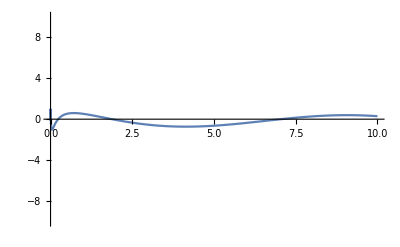

```mathematica
Plot[f[x],{x,-10,10},PlotRange->{-10,10}]
```

```mathematica
x/.FindRoot[f[x],{x,{0.1,1.5,7}}]
```

{0.233639,1.87954,7.04672}

```mathematica
Clear[f]
```

#### Задание 12.4

```mathematica
Reduce[x^2-6x+5<0,x]
```

1<x<5

```mathematica
Reduce[x^2-b*x+5<0,x]
```

(b<-2 √5&&b/2-1/2 √(-20+b^2)<x<b/2+1/2 √(-20+b^2))||(b>2 √5&&b/2-1/2 √(-20+b^2)<x<b/2+1/2 √(-20+b^2))

```mathematica
Plot[x^2-bx+5==0,{x,-10,10},{b,-10,10}]
```

Plot::nonopt: Options expected (instead of {b,-10,10}) beyond position 2 in Plot[x^2-bx+5==0,{x,-10,10},{b,-10,10}]. An option must be a rule or a list of rules.

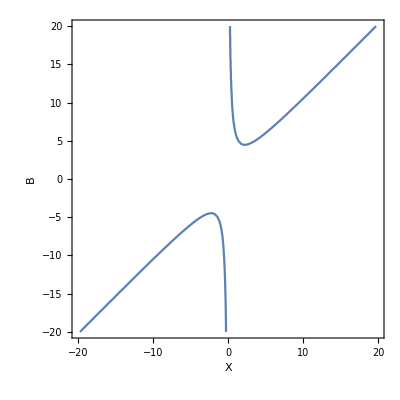

```mathematica
ContourPlot[x^2-b*x+5==0,{x,-20,20},{b,-20,20},FrameLabel->{"X","B"}]
```

#### Задание 12.5

```mathematica
sistema={x+a*y==b,x+b*y^2==a+b}
```

{x+a y==b,x+b y^2==a+b}

```mathematica
reshenie=Solve[sistema,{x,y}]
```

{{x→1/2 (-a^2/b+2 b+(a^(3/2) √(a+4 b))/b),y→(a-√a √(a+4 b))/(2 b)},{x→1/2 (-a^2/b+2 b-(a^(3/2) √(a+4 b))/b),y→(a+√a √(a+4 b))/(2 b)}}

```mathematica
sistema/.reshenie//Simplify
```

{{True,True},{True,True}}

```mathematica
Clear[sistema,reshenie]
```

```mathematica
sistema={Log[2/10,4*x-2*y]==-1,Log[x+2*y]==2}
```

{-Log[4 x-2 y]/Log[5]==-1,Log[x+2 y]==2}

```mathematica
{XX,YY}={x,y}/.Solve[sistema,{x,y}]//Flatten
```

{1/5 (5+ⅇ^2),1/10 (-5+4 ⅇ^2)}

```mathematica
XX^2+Sin[2*YY]//N
```

5.15926

```mathematica
Clear[XX,YY,sistema]
```

#### Задание 12.6

```mathematica
sistema={2*y+3*x^2==5,x+7*y^2==7.5}
```

{3 x^2+2 y==5,x+7 y^2==7.5}

```mathematica
YY=y/.NSolve[sistema,{x,y}]//Flatten
```

{-1.13749,0.962708,-0.924966,1.09975}

```mathematica
XX=x/.NSolve[sistema,{x,y}]//Flatten
```

{-1.55724,1.01235,1.51106,-0.966177}

```mathematica
ⅇ^XX⟦2⟧*Cos[YY⟦4⟧]
```

1.24894

```mathematica
Clear[XX,YY,sistema]
```

#### Задание 12.7

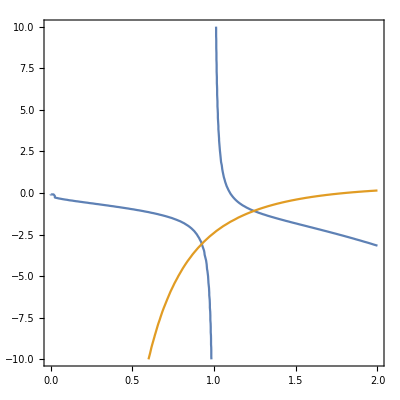

```mathematica
ContourPlot[{ⅇ^x+2*y*Log[x]-3==0,x^2*y-3*x+5.4==0},{x,0,2},{y,-10,10}]
```

```mathematica
FindRoot[{ⅇ^x+2*y*Log[x]-3==0,x^2*y-3*x+5.4==0},{{x,{0.9,1.2}},{y,{-3,-1}}}]
```

{x→{0.92504,1.24436},y→{-3.06752,-1.07653}}

#### Задание 12.8

```mathematica
Reduce[{5*x+12≤3*x+20,x<2*x+3,2*x+7≥0}, x]
```

-3<x≤4

```mathematica
Reduce[{y>x^2+1,y+x>1,x^2+y^2≤9}, {x,y}]
```

(Root-1.30Root[-8+3 #1^2+#1^4&,1]-1.30443938867102<x≤-1&&1+x^2<y≤√(9-x^2))||(-1<x≤0&&1-x<y≤√(9-x^2))||(0<x<Root1.30Root[-8+3 #1^2+#1^4&,2]1.30443938867102&&1+x^2<y≤√(9-x^2))

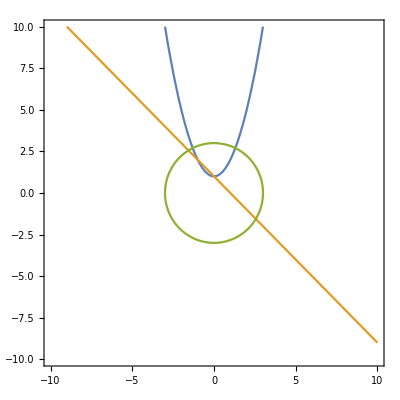

```mathematica
ContourPlot[{y==x^2+1,y+x==1,x^2+y^2==9},{x,-10,10},{y,-10,10},Axes->True]
```

### Решение дифференциальных уравнений

#### Задание 13.1

```mathematica
DSolveValue[y'[x]==2*Log[x]+x-2,y[x],x]
```

-4 x+x^2/2+C[1]+2 x Log[x]

```mathematica
DSolveValue[y'''[x]==3*x^2-2*x+1,y[x],x]
```

x^3/6-x^4/12+x^5/20+C[1]+x C[2]+x^2 C[3]

```mathematica
Clear[x,y]
```

#### Задание 13.2

```mathematica
sol=DSolve[{y''[x]==y[x],y[0]==1,y'[0]==0},y[x],x]
```

{{y[x]→1/2 ⅇ^-x (1+ⅇ^(2 x))}}

```mathematica
Y[x]=x/.sol
```

{x}

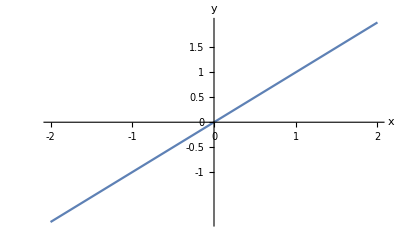

```mathematica
Plot[Y[x],{x,-2,2},AxesLabel->{"x","y"},Ticks->{{-2,-1,0,1,2},{-1,-0.5,0,0.5,1,1.5}}]
```

```mathematica
Clear[sol,Y,y]
```

```mathematica
DSolveValue[{y''[x]-2*ψ*y'[x]+ω^2*y[x]==0, y[0]==A,y'[0]==0},y[x],x]
```

(A (ⅇ^(x (ψ-√(ψ^2-ω^2))) ψ-ⅇ^(x (ψ+√(ψ^2-ω^2))) ψ+ⅇ^(x (ψ-√(ψ^2-ω^2))) √(ψ^2-ω^2)+ⅇ^(x (ψ+√(ψ^2-ω^2))) √(ψ^2-ω^2)))/(2 √(ψ^2-ω^2))

```mathematica
Y=DSolveValue[{y''[x]-2*ψ*y'[x]+ω^2*y[x]==0, y[0]==A,y'[0]==0},y[x],x]
```

(A (ⅇ^(x (ψ-√(ψ^2-ω^2))) ψ-ⅇ^(x (ψ+√(ψ^2-ω^2))) ψ+ⅇ^(x (ψ-√(ψ^2-ω^2))) √(ψ^2-ω^2)+ⅇ^(x (ψ+√(ψ^2-ω^2))) √(ψ^2-ω^2)))/(2 √(ψ^2-ω^2))

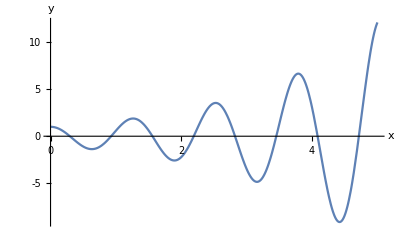

```mathematica
Plot[Y/.{A->1,ψ->0.5,ω->5},{x,0,5},AxesLabel->{"x","y"},Ticks->{{0,1,2,3,4,5},{-10,-5,0,5,10}}]
```

#### Задание 13.3

```mathematica
Clear[x,y]
sol=NDSolve[{y''[x]*y'[x]-x*y[x]==1,y[0]==1,y'[0]==1},y,{x,200}]
```

{{y→InterpolatingFunction[…]}}

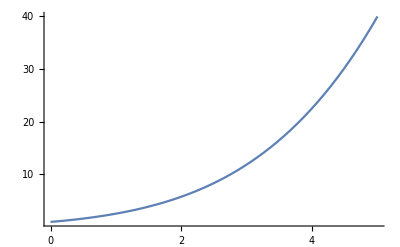

```mathematica
Plot[y[x]/.sol,{x,0,5},Ticks->{{0,1,2,3,4,5},{0,10,20,30,40}},PlotRange->All]
```

```mathematica
TableForm[Table[y[x]/.sol,{x,0,5,0.5}],Table[g[x]==x,{x,0,5,0.5}],TableHeadings->{"x","y"}]
```

1.
1.62927
2.55922
3.8926
5.7697
8.3605
11.8627
16.502
22.532
30.2354
39.9239

#### Задание 13.4

```mathematica
DSolve[{x'[t]==y[t]+z[t],y'[t]==x[t]+3*z[t],z'[t]==x[t]+y[t]},{x,y,z},t]
```

{{x→Function[{t},-(8 ⅇ^(-t-(√17 t)/2) (-√17 ⅇ^(3 t/2)+17 ⅇ^((√17 t)/2)+√17 ⅇ^((3 t)/2+√17 t)) C[1])/((-17+3 √17) (17+3 √17))-(8 √17 ⅇ^(t/2-(√17 t)/2) (-1+ⅇ^(√17 t)) C[2])/((-17+3 √17) (17+3 √17))+(4 ⅇ^(-t-(√17 t)/2) (-17 ⅇ^(3 t/2)-√17 ⅇ^(3 t/2)+34 ⅇ^((√17 t)/2)-17 ⅇ^((3 t)/2+√17 t)+√17 ⅇ^((3 t)/2+√17 t)) C[3])/((-17+3 √17) (17+3 √17))],y→Function[{t},(4 ⅇ^(-t-(√17 t)/2) (-17 ⅇ^(3 t/2)-√17 ⅇ^(3 t/2)+34 ⅇ^((√17 t)/2)-17 ⅇ^((3 t)/2+√17 t)+√17 ⅇ^((3 t)/2+√17 t)) C[1])/((-17+3 √17) (17+3 √17))+(4 ⅇ^(t/2-(√17 t)/2) (-17-√17-17 ⅇ^(√17 t)+√17 ⅇ^(√17 t)) C[2])/((-17+3 √17) (17+3 √17))-(4 ⅇ^(-t-(√17 t)/2) (-17 ⅇ^(3 t/2)-9 √17 ⅇ^(3 t/2)+34 ⅇ^((√17 t)/2)-17 ⅇ^((3 t)/2+√17 t)+9 √17 ⅇ^((3 t)/2+√17 t)) C[3])/((-17+3 √17) (17+3 √17))],z→Function[{t},-(8 √17 ⅇ^(t/2-(√17 t)/2) (-1+ⅇ^(√17 t)) C[1])/((-17+3 √17) (17+3 √17))-(8 √17 ⅇ^(t/2-(√17 t)/2) (-1+ⅇ^(√17 t)) C[2])/((-17+3 √17) (17+3 √17))+(4 ⅇ^(t/2-(√17 t)/2) (-17-√17-17 ⅇ^(√17 t)+√17 ⅇ^(√17 t)) C[3])/((-17+3 √17) (17+3 √17))]}}

```mathematica
DSolveValue[{x'[t]==y[t]+z[t],y'[t]==x[t]+3*z[t],z'[t]==x[t]+y[t]},{x,y,z},t]
```

{Function[{t},-(8 ⅇ^(-t-(√17 t)/2) (-√17 ⅇ^(3 t/2)+17 ⅇ^((√17 t)/2)+√17 ⅇ^((3 t)/2+√17 t)) C[1])/((-17+3 √17) (17+3 √17))-(8 √17 ⅇ^(t/2-(√17 t)/2) (-1+ⅇ^(√17 t)) C[2])/((-17+3 √17) (17+3 √17))+(4 ⅇ^(-t-(√17 t)/2) (-17 ⅇ^(3 t/2)-√17 ⅇ^(3 t/2)+34 ⅇ^((√17 t)/2)-17 ⅇ^((3 t)/2+√17 t)+√17 ⅇ^((3 t)/2+√17 t)) C[3])/((-17+3 √17) (17+3 √17))],Function[{t},(4 ⅇ^(-t-(√17 t)/2) (-17 ⅇ^(3 t/2)-√17 ⅇ^(3 t/2)+34 ⅇ^((√17 t)/2)-17 ⅇ^((3 t)/2+√17 t)+√17 ⅇ^((3 t)/2+√17 t)) C[1])/((-17+3 √17) (17+3 √17))+(4 ⅇ^(t/2-(√17 t)/2) (-17-√17-17 ⅇ^(√17 t)+√17 ⅇ^(√17 t)) C[2])/((-17+3 √17) (17+3 √17))-(4 ⅇ^(-t-(√17 t)/2) (-17 ⅇ^(3 t/2)-9 √17 ⅇ^(3 t/2)+34 ⅇ^((√17 t)/2)-17 ⅇ^((3 t)/2+√17 t)+9 √17 ⅇ^((3 t)/2+√17 t)) C[3])/((-17+3 √17) (17+3 √17))],Function[{t},-(8 √17 ⅇ^(t/2-(√17 t)/2) (-1+ⅇ^(√17 t)) C[1])/((-17+3 √17) (17+3 √17))-(8 √17 ⅇ^(t/2-(√17 t)/2) (-1+ⅇ^(√17 t)) C[2])/((-17+3 √17) (17+3 √17))+(4 ⅇ^(t/2-(√17 t)/2) (-17-√17-17 ⅇ^(√17 t)+√17 ⅇ^(√17 t)) C[3])/((-17+3 √17) (17+3 √17))]}

#### Задание 13.5

```mathematica
Clear[X,Y,sol]
sol=DSolveValue[{x'[t]==-a*x[t]+m*y[t],y'[t]==a*x[t]-m*y[t],x[0]==1,y[0]==0},{x,y},t]
```

{Function[{t},(a ⅇ^((-a-m) t)+m)/(a+m)],Function[{t},-(a (-1+ⅇ^((-a-m) t)))/(a+m)]}

```mathematica
{X,Y}=DSolveValue[{x'[t]==-a*x[t]+m*y[t],y'[t]==a*x[t]-m*y[t],x[0]==1,y[0]==0},{x,y},t]/.{a->2,m->1/4}
```

{Function[{t},(2 ⅇ^((-2-1/4) t)+1/4)/(2+1/4)],Function[{t},-(2 (-1+ⅇ^((-2-1/4) t)))/(2+1/4)]}

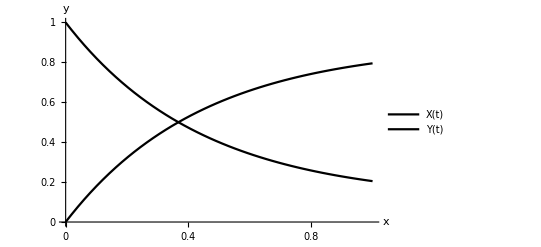

```mathematica
Plot[{X[t],Y[t]},{t,0,1}, Ticks->{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},AxesLabel->{"x","y"},PlotLegends->{"X(t)","Y(t)"},AxesStyle->FontSize->14,PlotStyle->{{Thin, Black},{Thick, Black}}]
```

```mathematica
Clear[X,Y,sol]
```

#### Задание 13.6

```mathematica
DSolveValue[{x'[t]==y[t]*z[t]+1,y'[t]==x[t]*z[t]-1,z'[t]==x[t]*y[t]+1,x[0]==1,y[0]==0,z[0]==0},{x[t],y[t],z[t]},{t,0,20}]
```

DSolveValue[{x'[t]==1+y[t] z[t],y'[t]==-1+x[t] z[t],z'[t]==1+x[t] y[t],x[0]==1,y[0]==0,z[0]==0},{x[t],y[t],z[t]},{t,0,20}]

```mathematica
{X,Y,Z}=
```